```mathematica
ℏc=1973/10000;c=(169 π^2)/360;  A=197; ρ0=17/100; R=637/100; ξ=54/100; σ=4; b=0;
T[x_?NumericQ,y_?NumericQ]:=NIntegrate[ρ0/(1+Exp[(√(x^2+y^2+z^2)-R)/ξ]),{z,-∞,∞}];
e[x_,y_]:=T[x+b/2,y](1-(1-σ/A T[x-b/2,y])^A)+T[x-b/2,y](1-(1-σ/A T[x+b/2,y])^A);
Temp[x_,y_]:=((30e[x,y])/(3c ℏc e[0,0]))^(1/4);
```

```mathematica
197.3(0.516/(3c (0.1973)))^(1/4)
```

129.944

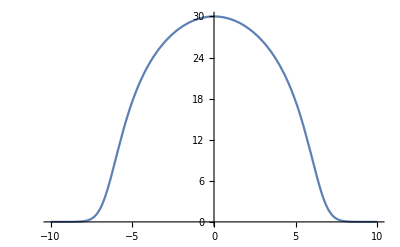

```mathematica
Plot[30 e[x,0]/e[0,0],{x,-10,10}]
```

```mathematica
30 e[7.459666578962809,0]/e[0,0]
```

0.516

```mathematica
FindRoot[30 e[r,0]/e[0,0]==516/1000,{r,7}]//Quiet
```

{r→7.45967}

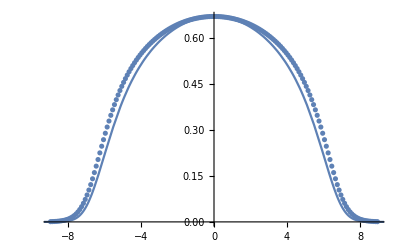

```mathematica
data=ArrayReshape[ReadList["C:\\Users\\chris\\Downloads\\techqm.txt",Real],{25423,3}];
Show[ListPlot[Select[data,(#[[1]]==0.05)&][[;;,{2,3}]]],Plot[{0.15449880487641732e[1/20,x]},{x,-10,10}]]
```

```mathematica
(16+26+1/4)π^2/90
```

(169 π^2)/360